Conjecture: Suppose p[i] is the i-th prime,  p[1]=2,
g[i]=p[i + 1] - p[i], 
h[1]=g[1], h[n] = g[1]-g[2]+g[3]-g[4]+...+ (-1)^(n-1) g[n] = h[n-1]+(-1)^(n-1) g[n],
then {h[n]} changes sign infinitely often, however lazily, and h[n] never just equal to 0, for n=1,2,3,...

```mathematica
Block[{$RecursionLimit=2000},
g[i_]:=Prime[i+1]-Prime[i];
h[0]=0;
h[n_]:=h[n-1]+(-1)^(n-1)g[n];
list=Table[h[i],{i,1,400}]

]
```

{1,-1,1,-3,-1,-5,-3,-7,-1,-3,3,-1,1,-3,3,-3,-1,-7,-3,-5,1,-3,3,-5,-1,-3,1,-1,3,-11,-7,-13,-11,-21,-19,-25,-19,-23,-17,-23,-21,-31,-29,-33,-31,-43,-31,-35,-33,-37,-31,-33,-23,-29,-23,-29,-27,-33,-29,-31,-21,-35,-31,-33,-29,-43,-37,-47,-45,-49,-43,-51,-45,-51,-47,-53,-45,-49,-41,-51,-49,-59,-57,-63,-59,-65,-57,-61,-59,-63,-51,-59,-55,-63,-59,-65,-53,-55,-37,-43,-33,-39,-33,-35,-29,-39,-33,-39,-37,-43,-37,-41,-39,-51,-41,-43,-39,-45,-39,-41,-29,-33,-27,-35,-25,-33,-23,-31,-25,-31,-27,-35,-29,-33,-25,-29,-15,-25,-13,-15,-5,-7,-3,-5,5,-9,-5,-7,-3,-17,-13,-15,-11,-31,-27,-35,-25,-33,-29,-35,-29,-43,-39,-45,-39,-47,-41,-53,-49,-55,-53,-63,-61,-67,-57,-59,-49,-51,-45,-63,-59,-61,-57,-63,-57,-65,-59,-65,-43,-45,-35,-43,-33,-39,-33,-41,-29,-33,-27,-33,-31,-37,-25,-35,-17,-19,-15,-21,-19,-25,-21,-23,-19,-31,-29,-35,-1,-7,-1,-9,9,-1,13,9,11,7,13,5,9,7,13,1,11,9,13,11,15,9,21,9,17,5,11,7,13,5,9,1,5,-9,-5,-11,-9,-13,-7,-9,-3,-13,7,1,5,3,27,23,25,15,27,25,35,27,33,27,33,15,21,17,19,7,17,5,13,-3,11,5,9,7,11,9,19,7,13,7,25,23,39,37,59,53,61,55,59,57,61,53,59,49,51,41,55,45,51,39,41,37,39,29,41,39,55,53,59,55,57,47,55,37,61,57,63,55,71,69,73,65,81,79,83,75,81,75,79,67,69,47,53,51,57,53,59,45,51,47,49,43,47,41,53,47,53,39,43,37,49,41,47,43,69,51,61,53,57,51,53,47,69,57,59,43,51,47,59,45,55,53,57,49,55,49,53,51,55,49,57,53,55,49,59,57,67,59}

This conjecture is to say that the followed curve intersects the line y=x infinitely often.

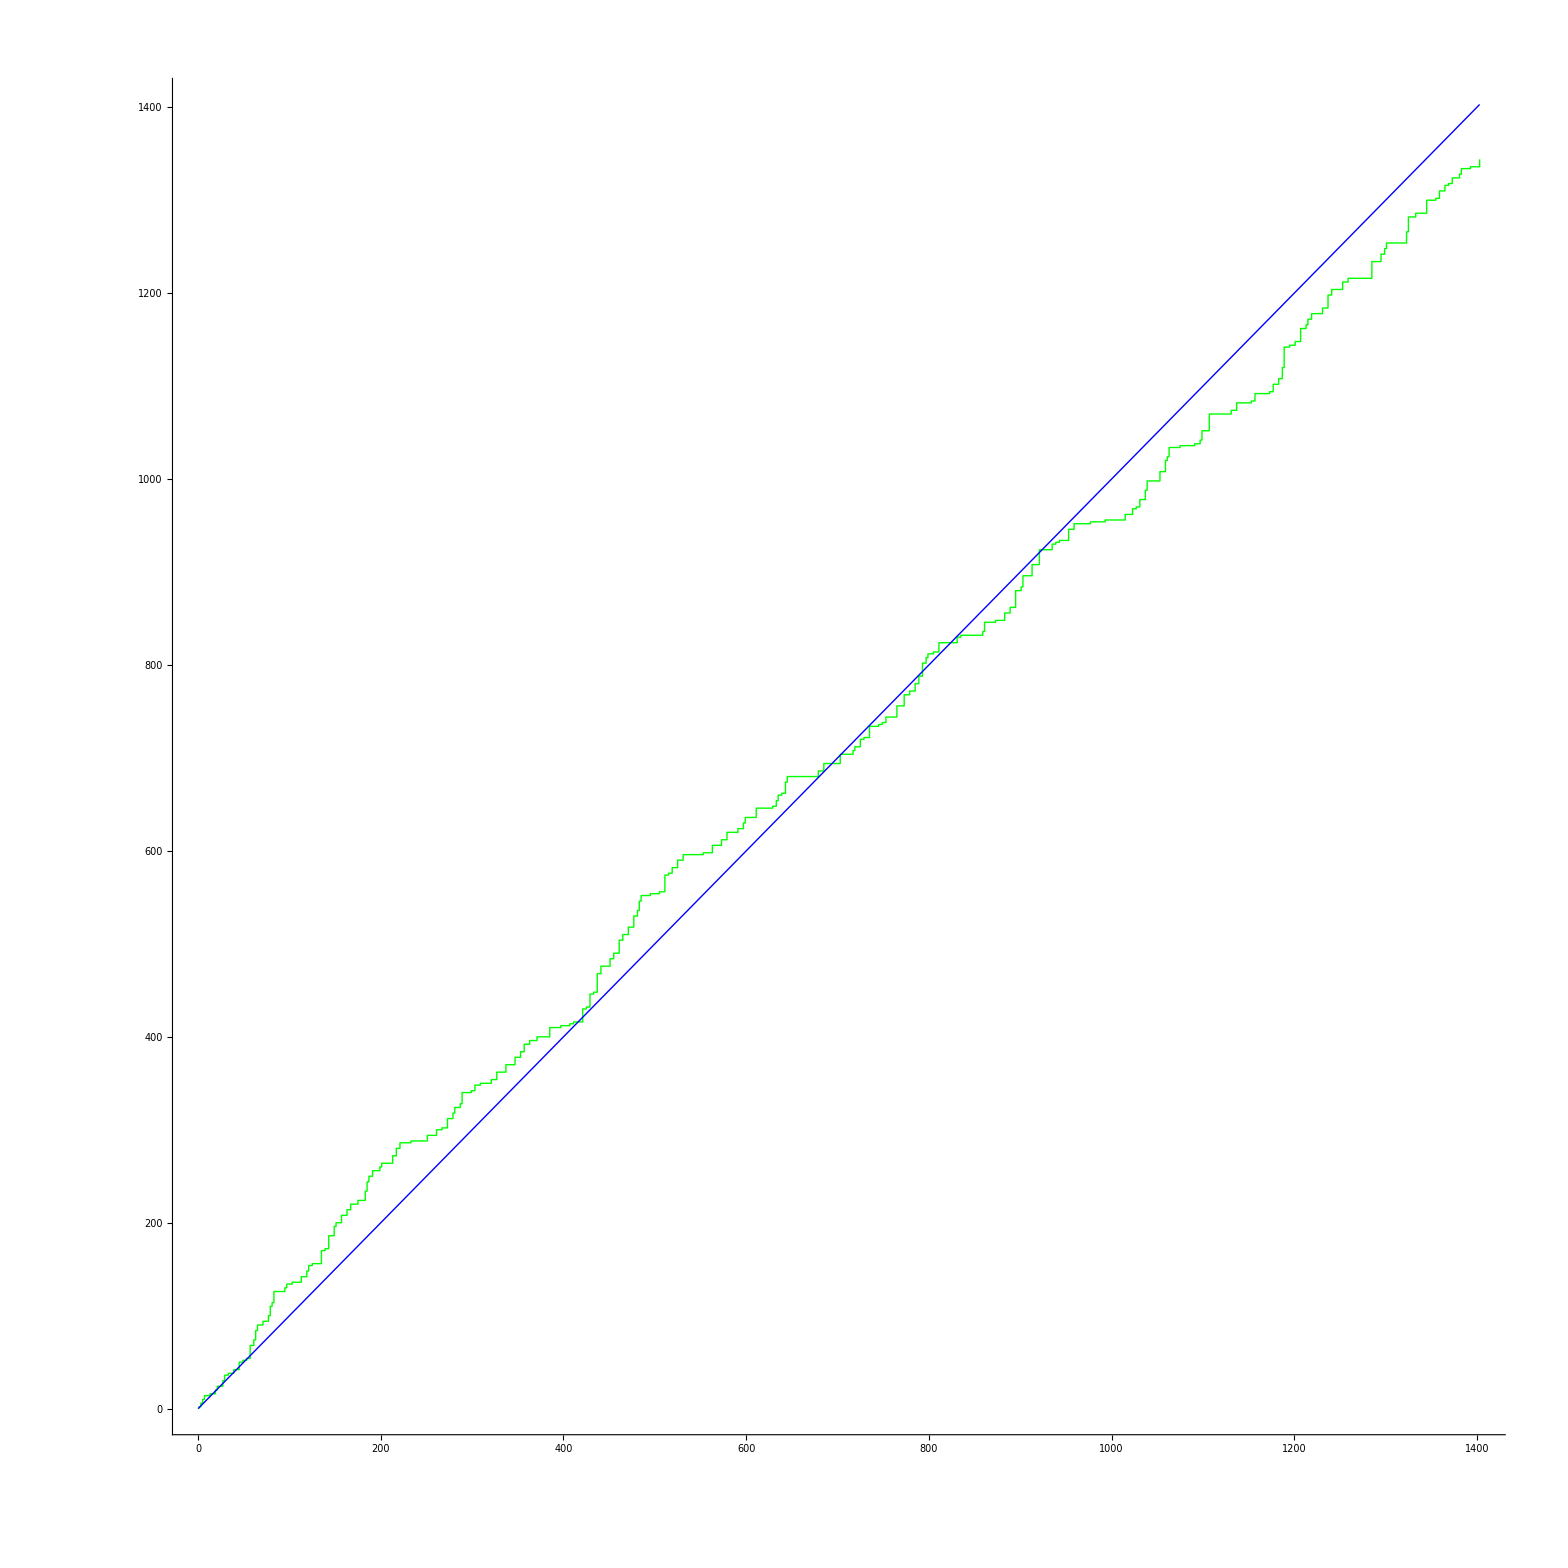

```mathematica
Block[{$RecursionLimit=1000},
pt[0]={0,0};
pt[j_Integer]:=pt[j-1]+If[OddQ[j],{Prime[j+1]-Prime[j],0},{0,Prime[j+1]-Prime[j]}];
n=400;
Graphics[{Green,Line[Table[pt[i],{i,1,n}]],Blue,Line[{{0,0},{pt[n][[1]],pt[n][[1]]}}]},Axes->True]
]
```